### Definitions

```mathematica
(*Define particle Number Np, number of dimensions d, modes m natural length scales in terms of kappa (=k) as well as coordinates*)
Np=2
d = 1;
lm = 1;
lp[k_]:=((k+1)^(-1/4))/lm;
$Assumptions = -1<k && Im[k]==0
xcoord={x1,x2,x3}
xpcoord = {x1p,x2p,x3p}
```

2

-1<k&&Im[k]==0

{x1,x2,x3}

{x1p,x2p,x3p}

```mathematica
(*Np is the number of fermions; d is the dimension; define p and q as in 2.25 of Harmonium1 document; 'a' and 'b' denote A and Subscript[B, N] of the Harmonium1 document*)
p[a_,b_, Np_]:=Sqrt[b/(a-b(Np-1))];
q2[x_,a_,b_,x1_,x2_,x1p_,x2p_, Np_]:=Sqrt[2a](x-b/(2(a-b(Np-1)))(x1+x2+x1p+x2p));
```

```mathematica
(*Define A, Subscript[B, N] and the natural length in terms of l_+=lp and l_-=s*)
A[lp_]:=1/(2 lp^2);
B[lm_,lp_, Np_]:=-1/(2Np) (1/lm^2-1/lp^2);
l[lm_,lp_, Np_]:=1/((((Np-1) lm^2+lp^2)/(lm^4 lp^2+(Np-1) lm^2 lp^4))^(1/4))
f[a_,b_,Np_] := ((Np-2)*b^2/2)/(a-(Np-2)b)-((Np-1)*b^2/2)/(a-(Np-1)b);
```

```mathematica
(*Define c and d of Mehler's formular, see 2.28 in Harmonium1 document; here c is c and d0 is d*)
c[s_,t_, Np_]:=Sqrt[Np/((Np-1) t^2+s^2)];
d0[s_,t_, Np_]:=Sqrt[((Np-1) s^2 +t^2)/(Np s^2 t^2)];
```

```mathematica
(*Define the q parameter in Mehler's formula, see 2.29 of Harmonium1 document*)
Q[s_,t_, Np_]:=(d0[s,t,Np]-c[s,t,Np])/(d0[s,t,Np]+c[s,t,Np]);
```

### Defining Exponential Functions, Normalization and HF Basis Functions

```mathematica
efun2[a_,b_, x1_, x2_]:=Exp[-a(x1^2+x2^2)+b(x1+x2)^2];
efun2poly[a_,b_, x1_, x2_, x3_]:=-a(x1^2+x2^2+x1p^2+x2p^2)+b(x1+x2)^2+b(x1p+x2p)^2;
efun1[a_,b_, x1_, x1p_]:=Exp[-(a-b-b^2(Np-1)/(2(a-b(Np-1))))(x1^2+x1p^2)]*Exp[b^2(Np-1)/(a-b(Np-1)) x1* x1p];
efun1poly[a_,b_]:=-(a-b-b^2(Np-1)/(2(a-b(Np-1))))(x1^2+x1p^2)+(b^2(Np-1)/(a-b(Np-1)) x1* x1p)
```

```mathematica
(*Integrate[efun2[a,b, x1, x2]*efun2[a,b,x1,x2],{x1,-∞,+∞},{x2,-∞,+∞}, Assumptions-> a>0 && b<0 ]*)
```

```mathematica
(*Integrate[efun1[a,b,x1,x1],{x1,-∞,+∞}, Assumptions-> a>0 && b<0 ]*)
(*Integrate[efun1[a,b, x1, x1],{x1,-∞,+∞}, Assumptions-> a>0 && b<0 ]*)
```

```mathematica
(*Integrate[efunana2rdo[a,b,Np,x1,x1, x2, x2],{x1,-∞,+∞}, {x2,-∞,+∞},Assumptions-> a>0 && Im[a]==Im[b]==0]*)
```

```mathematica
(*Integrate[efun1rdo[a,b, x1,x1, x2, x2, Np],{x1,-∞,+∞}, {x2,-∞,+∞}, Assumptions-> a>0 && b<0 && Np∈PositiveIntegers ]*)
```

```mathematica
norm2rdopre[a_,b_, Np_]:=(π/(2 √(a (a-2 b))))^(-1)
norm2rdo[lm_,lp_, Np_]:=norm2rdoPre[A[lp],B[lm,lp, Np], Np];
```

```mathematica
norm1rdopre[a_,b_, Np_]:=(√((a π-b π)/(2 a^2-4 a b)))^(-1)
norm1rdo[lm_,lp_, Np_]:=norm1rdoPre[A[lp],B[lm,lp, Np], Np];
```

```mathematica
(*define 2 particle hf basis*)
(*define 2 particle hf basis*)
hfcoef[n_,x_, a_]:=(Factorial[n]2^n π^(1/2)  )^(-1/2)*(2*a)^(1/4)* HermiteH[n,(x*Sqrt[2a])]
hf2basis[m1_, m2_, n1_,n2_,a_]:=1/2(hfcoef[m1,x1,a]*hfcoef[m2,x2, a]+hfcoef[m2,x1,a]*hfcoef[m1,x2,a])*1/2(hfcoef[n1,x1p,a]*hfcoef[n2,x2p,a]+hfcoef[n2,x1p,a]*hfcoef[n1,x2p,a])
hf1basis[m1_, n1_,a_]:=(hfcoef[m1,x1,a]*hfcoef[n1,x1p,a])
```

### Determining the coefficients of the Polynomial Contribution to the integral

```mathematica
(*Determine the coefficients of the polynomial 'hfibasis' by the coefficientlist function where q corresponds to the power, i.e. x^q , importantly this is not the mathematica index*)
```

```mathematica
coefstart2[m1_, m2_, n1_,n2_,x_,q_,a_] :=CoefficientList[hf2basis[m1,m2,n1,n2,a], x][[q+1]]
maxdegreestart2[m1_,m2_,n1_,n2_, x_] := Length[CoefficientList[hf2basis[m1,m2,n1,n2,a], x]]-1
constantstart2[m1_, m2_, n1_,n2_,x_] := coefstart2[m1, m2, n1,n2,x,1,a]

coefstart1[m1_, n1_,x_,q_,a_] :=CoefficientList[hf1basis[m1,n1,a], x][[q+1]]
maxdegreestart1[m1_,n1_, x_] := Length[CoefficientList[hf1basis[m1,n1,a], x]]-1
constantstart1[m1_, n1_,x_] := coefstart1[m1, n1,x,1,a]
```

```mathematica
coefstart2[2,2,2,2,x1,1,a]
```

0

```mathematica
Sum[coefstart2[5,5,2,5,x1,q,a]*x1^q,{q,0,maxdegreestart2[5,5,2,5,x1]}]-hf2basis[5,5,2,5,a]//Simplify
```

0

### Integrating coefficient by coefficient and determining helper functions/exponential polynomials

```mathematica
polycoef[poly_, x_,q_]:= CoefficientList[poly, x][[q+1]]
maxdegreepoly[poly_, x_]:=Length[CoefficientList[poly, x]]-1
```

```mathematica
exppolyinit2=-2a*(x1^2+x2^2+x1p^2+x2p^2)+b((x1+x2)^2+(x1p+x2p)^2);
```

```mathematica
exppolyinit1 = efun1poly[a,b]-a(x1^2+x1p^2)
```

(b^2 x1 x1p)/(a-b)-a (x1^2+x1p^2)+(-a+b+b^2/(2 (a-b))) (x1^2+x1p^2)

```mathematica
efuncoef[exppoly_, x_,q_] :=CoefficientList[exppoly, x][[q+1]];
```

```mathematica
intxmab[m_, a_, b_]:=1/2 (-a)^(-m/2) (1/a(-1+(-1)^m) b Gamma[1+m/2] Hypergeometric1F1[1+m/2,3/2,-b^2/(4 a)]+((1+(-1)^m) Gamma[(1+m)/2] Hypergeometric1F1[(1+m)/2,1/2,-b^2/(4 a)])/(√-a))
intxmabpoly[m_,a_,b_]:=intxmab[m,a,b]*Exp[(b^2)/(4a)]
```

```mathematica
intexppoly[a_,b_]:=-(b^2)/(4a)
```

```mathematica
int2poly[m1_,m2_,n1_,n2_]:= Sum[coefstart2[m1,m2,n1,n2,x1, q, a ]*intxmabpoly[q,efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]], {q,0, maxdegreestart2[m1,m2,n1,n2, x1]}]
int1poly[m1_,n1_]:= Sum[coefstart1[m1,n1,x1, q, a ]*intxmabpoly[q,efuncoef[exppolyinit1, x1, 2], efuncoef[exppolyinit1, x1, 1]], {q,0, maxdegreestart1[m1,n1, x1]}]
```

```mathematica
intgenpoly[ poly_, exppoly_, xint_]:= Sum[polycoef[poly,xint, q ]*intxmabpoly[q,efuncoef[exppoly, xint, 2], efuncoef[exppoly, xint, 1]], {q,0, maxdegreepoly[poly, xint]}]
```

## Running the algorithm for the various particle sectors

```mathematica
mode1 = 0;
mode2 =1;
```

### Run algorithm for 1 RDO diag mode1

```mathematica
polym1 = int1poly[mode1, mode1];
exppolym1= efuncoef[exppolyinit1, x1, 0]+ intexppoly[efuncoef[exppolyinit1, x1, 2], efuncoef[exppolyinit1, x1, 1]] // Simplify
```

-(2 a (4 a^2-8 a b+3 b^2) x1p^2)/(4 a^2-6 a b+b^2)

```mathematica
polym2 = intgenpoly[polym1, exppolym1, x1p] // Simplify
exppolym2 = efuncoef[exppolym1, x1p, 0]+ intexppoly[efuncoef[exppolym1, x1p, 2], efuncoef[exppolym1, x1p, 1]] // Simplify
```

(√a)/(√((a (4 a^2-8 a b+3 b^2))/(4 a^2-6 a b+b^2)) √((4 a^2-6 a b+b^2)/(2 a π-2 b π)))

0

```mathematica
intd11=norm1rdopre[a,b,Np]* polym2*Exp[exppolym2]
```

(√a)/(√((a (4 a^2-8 a b+3 b^2))/(4 a^2-6 a b+b^2)) √((4 a^2-6 a b+b^2)/(2 a π-2 b π)) √((a π-b π)/(2 a^2-4 a b)))

### Run algorithm for 1 RDO diag mode2

```mathematica
polym1 = int1poly[mode2, mode2];
exppolym1= efuncoef[exppolyinit1, x1, 0]+ intexppoly[efuncoef[exppolyinit1, x1, 2], efuncoef[exppolyinit1, x1, 1]] // Simplify
```

-(2 a (4 a^2-8 a b+3 b^2) x1p^2)/(4 a^2-6 a b+b^2)

```mathematica
polym2 = intgenpoly[polym1, exppolym1, x1p] // Simplify
exppolym2 = efuncoef[exppolym1, x1p, 0]+ intexppoly[efuncoef[exppolym1, x1p, 2], efuncoef[exppolym1, x1p, 1]] // Simplify
```

(a^(3/2) b^2)/(((a (4 a^2-8 a b+3 b^2))/(4 a^2-6 a b+b^2))^(3/2) ((4 a^2-6 a b+b^2)/(2 a π-2 b π))^(3/2) (2 a π-2 b π))

0

```mathematica
intd12 =norm1rdopre[a,b,Np]* polym2*Exp[exppolym2]
```

(a^(3/2) b^2)/(((a (4 a^2-8 a b+3 b^2))/(4 a^2-6 a b+b^2))^(3/2) ((4 a^2-6 a b+b^2)/(2 a π-2 b π))^(3/2) (2 a π-2 b π) √((a π-b π)/(2 a^2-4 a b)))

```mathematica
2
```

2

### Run algorithm for 1 RDO offdiag mode1mode2

```mathematica
polym1 = int1poly[mode1, mode2];
exppolym1= efuncoef[exppolyinit1, x1, 0]+ intexppoly[efuncoef[exppolyinit1, x1, 2], efuncoef[exppolyinit1, x1, 1]] // Simplify
```

-(2 a (4 a^2-8 a b+3 b^2) x1p^2)/(4 a^2-6 a b+b^2)

```mathematica
polym2 = intgenpoly[polym1, exppolym1, x1p] // Simplify
exppolym2 = efuncoef[exppolym1, x1p, 0]+ intexppoly[efuncoef[exppolym1, x1p, 2], efuncoef[exppolym1, x1p, 1]] // Simplify
```

0

0

```mathematica
into1=norm1rdopre[a,b,Np]* polym2*Exp[exppolym2]
```

0

### Run algorithm for 2 RDO diag mode1mode1

```mathematica
polymm1 = int2poly[mode1, mode1, mode1, mode1];
```

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
intd21 = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

(√(a (a-2 b)))/(a-b)

### Run algorithm for 2 RDO diag mode2mode2

```mathematica
polymm1 = int2poly[mode2, mode2, mode2, mode2];
```

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
intd23 = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

(√(a (a-2 b)) b^2)/(4 (a-b)^3)

### Run algorithm for 2 RDO diag mode1mode2

```mathematica
polymm1 = int2poly[mode1, mode2, mode1, mode2];
```

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
intd22 = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

0

### Run algorithm for 2 RDO offdiag mode1mode1mode2mode2

```mathematica
polymm1 = int2poly[mode1, mode1, mode2, mode2];
```

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
into22 = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

(√(a (a-2 b)) b)/(2 (a-b)^2)

### Run algorithm for 2 RDO offdiag mode1mode1mode1mode2

```mathematica
polymm1 = int2poly[mode1, mode1, mode1, mode2]
```

(√a (2 a √(2/π) x1p+2 a √(2/π) x2p))/(√2 √(2 a-b))

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
into21 = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

0

### Run algorithm for 2 RDO offdiag mode1mode2mode2mode2

```mathematica
polymm1 = int2poly[mode1, mode2, mode2, mode2];
```

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
into23 = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

0

### Results

```mathematica
d21= intd21//Simplify
```

(√(a (a-2 b)))/(a-b)

```mathematica
d22 = intd22 //Simplify
```

0

```mathematica
d23  = intd23//Simplify
```

(√(a (a-2 b)) b^2)/(4 (a-b)^3)

```mathematica
o21 = into21//Simplify
```

0

```mathematica
o22 = into22//Simplify
```

(√(a (a-2 b)) b)/(2 (a-b)^2)

```mathematica
o23 = into23//Simplify
```

0

```mathematica
d11 = intd11-intd21-intd22 //Simplify
```

-(√(a (a-2 b)))/(a-b)+(2 √a)/(√((a-b)/(a^2-2 a b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (4 a^2-8 a b+3 b^2))/(4 a^2-6 a b+b^2)))

```mathematica
d12 = intd12-intd23-intd22 //Simplify
```

1/4 b^2 (-(√(a (a-2 b)))/(a-b)^3+(8 a^(3/2))/((a-b) √((a-b)/(a^2-2 a b)) ((4 a^2-6 a b+b^2)/(a-b))^(3/2) ((a (4 a^2-8 a b+3 b^2))/(4 a^2-6 a b+b^2))^(3/2)))

```mathematica
o1 = into1-into21 -into23//Simplify
```

0

```mathematica
-(√(a (a-2 b)) b)/(2 (a-b)^2)
```

-(√(a (a-2 b)) b)/(2 (a-b)^2)

```mathematica
pfinal[a_,b_]:=-(√(a (a-2 b)) b)/(2 (a-b)^2)
```

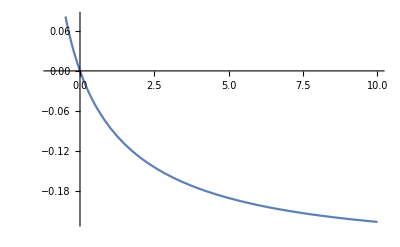

```mathematica
Plot[pfinal[A[lp[k]], B[lm,lp[k],Np]], {k,-0.99,10}]
```

```mathematica
{{d21,o21,o22},{o21,d22,o23}, {o22,o23,d23}}
```

{{(√(a (a-2 b)))/(a-b),0,(√(a (a-2 b)) b)/(2 (a-b)^2)},{0,0,0},{(√(a (a-2 b)) b)/(2 (a-b)^2),0,(√(a (a-2 b)) b^2)/(4 (a-b)^3)}}

```mathematica
{{d11,o1},{o1,d12}}
```

{{-(√(a (a-2 b)))/(a-b)+(2 √a)/(√((a-b)/(a^2-2 a b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (4 a^2-8 a b+3 b^2))/(4 a^2-6 a b+b^2))),0},{0,1/4 b^2 (-(√(a (a-2 b)))/(a-b)^3+(8 a^(3/2))/((a-b) √((a-b)/(a^2-2 a b)) ((4 a^2-6 a b+b^2)/(a-b))^(3/2) ((a (4 a^2-8 a b+3 b^2))/(4 a^2-6 a b+b^2))^(3/2)))}}

```mathematica
1-d11-d12-d21-d22-d23
```

1-(√(a (a-2 b)) b^2)/(4 (a-b)^3)-(2 √a)/(√((a-b)/(a^2-2 a b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (4 a^2-8 a b+3 b^2))/(4 a^2-6 a b+b^2)))-1/4 b^2 (-(√(a (a-2 b)))/(a-b)^3+(8 a^(3/2))/((a-b) √((a-b)/(a^2-2 a b)) ((4 a^2-6 a b+b^2)/(a-b))^(3/2) ((a (4 a^2-8 a b+3 b^2))/(4 a^2-6 a b+b^2))^(3/2)))

### Create Density Operator for MMRDO

```mathematica
matrixvac[a_,b_]:= 1-(√(a (a-2 b)) b^2)/(4 (a-b)^3)-(2 √a)/(√((a-b)/(a^2-2 a b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (4 a^2-8 a b+3 b^2))/(4 a^2-6 a b+b^2)))-1/4 b^2 (-(√(a (a-2 b)))/(a-b)^3+(8 a^(3/2))/((a-b) √((a-b)/(a^2-2 a b)) ((4 a^2-6 a b+b^2)/(a-b))^(3/2) ((a (4 a^2-8 a b+3 b^2))/(4 a^2-6 a b+b^2))^(3/2)))
```

```mathematica
matrixone[a_,b_]:={{-(√(a (a-2 b)))/(a-b)+(2 √a)/(√((a-b)/(a^2-2 a b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (4 a^2-8 a b+3 b^2))/(4 a^2-6 a b+b^2))),0},{0,1/4 b^2 (-(√(a (a-2 b)))/(a-b)^3+(8 a^(3/2))/((a-b) √((a-b)/(a^2-2 a b)) ((4 a^2-6 a b+b^2)/(a-b))^(3/2) ((a (4 a^2-8 a b+3 b^2))/(4 a^2-6 a b+b^2))^(3/2)))}}
```

```mathematica
Eigenvalues[matrixone[A[lp[50.5]], B[lm,lp[50.5],Np]]]
```

{0.052419,0.0242758}

```mathematica
matrixtwo[a_,b_]:={{(√(a (a-2 b)))/(a-b),0,(√(a (a-2 b)) b)/(2 (a-b)^2)},{0,0,0},{(√(a (a-2 b)) b)/(2 (a-b)^2),0,(√(a (a-2 b)) b^2)/(4 (a-b)^3)}}
```

```mathematica
Eigenvalues[matrixtwo[A[lp[60]], B[lm,lp[60],Np]]]
```

{(61^(1/4) (155+3 √61))/(1+√61)^3,0,0}

```mathematica
matrixdim={{0,0,0},{0,0,0},{0,0,0}}
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
fullmatrix[k_]:=Fold[ArrayFlatten[{{#,0},{0,#2}}]&,matrixvac[A[lp[k]], B[lm,lp[k],Np]],{matrixone[A[lp[k]], B[lm,lp[k],Np]],matrixtwo[A[lp[k]], B[lm,lp[k],Np]], matrixdim}]
```

```mathematica
Eigenvalues[fullmatrix[-0.8]]
```

{0.957885,0.0228527,0.01733,0.00193209,0.,0.,0.,0.,0.}

```mathematica
fullmatrix[-0.99] //MatrixForm
```

(0.243258 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.0551375 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.0304222 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.57496 | 0 | -0.235211 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.235211 | 0 | 0.0962226 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
matexportfunct[i_, ind_]:=Export["/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/"<>"data_m01_k"<>ToString[ind]<>".mat", fullmatrix[i]]
```

```mathematica
kappalogrange[i_]:= If[i≤1, i, 10^(i-1)]
kappamin = -0.99;
kappamax = 6;
kappagran = 0.1;
kappalist = Table[kappalogrange[k], {k,kappamin, kappamax, kappagran}];
```

```mathematica
Table[matexportfunct[kappalist[[i]],i],{i,1,Length[kappalist]}]
```

{/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k1.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k2.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k3.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k4.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k5.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k6.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k7.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k8.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k9.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k10.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k11.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k12.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k13.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k14.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k15.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k16.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k17.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k18.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k19.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k20.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k21.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k22.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k23.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k24.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k25.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k26.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k27.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k28.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k29.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k30.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k31.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k32.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k33.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k34.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k35.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k36.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k37.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k38.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k39.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k40.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k41.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k42.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k43.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k44.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k45.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k46.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k47.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k48.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k49.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k50.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k51.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k52.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k53.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k54.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k55.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k56.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k57.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k58.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k59.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k60.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k61.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k62.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k63.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k64.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k65.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k66.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k67.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k68.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k69.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n2d1_m01/data_m01_k70.mat}